# DRIMA:

### Pedro Paulo Balbi de Oliveira^©, 11-March-2017 Universidade Presbiteriana Mackenzie

## Acknowledgements and “To Do” list

Acknowledgements:
The implementation and conception of DRIMA has benefitted from distinct contributions of my students who used it. Most notably, I express my gratitude to Tiago Guglielmeti Correale, with whom I defined the present vectorial interaction of the system and who provided its first implementation. Previously, Vinícius Osiro Medeiros had taken the very first steps in the vectorial scheme, even though in a preliminary conception and implementation that is now superseded. Finally, José Antonio Poiani’s extensive use of DRIMA was essential to its original conception and debugging of the first implementation.

To Do:
(1) ???

## Initial set-up

```mathematica
$DRIMA="/Users/PP/Dropbox/PP/TALKS/2020 Conferência Virtual Brasileira de Tecnologia Wolfram/";
```

## General

Example of a world with 3 agents:   { {agent1 , agent2, agent3}, {xmax, ymax}, mobility }
where
agent1 is {{"D1", {0., 1., 0., 0., 0., 0., 0., 0., 0.}, {}}, {4, 1}}
agent2 is {{"D2", {0., 0., 0., 0., 0., 1., 0., 0., 0.}, {}}, {2, 3}}
agent3 is {{"R1", {0.11, 0.11, 0.11, 0.11, 0.11, 0.11, 0.11,  0.11, 0.11}, {}} , {3,3}}
{xmax, ymax} is the gridworld size
mobility is either F (full) or P (partial)

```mathematica
AgName[agent_]:=agent⟦1,1⟧;
AgType[agent_]:=StringTake[agent⟦1,1⟧,1];
AgMovPattern[agent_]:=agent⟦1,2⟧;
AgProps[agent_]:=agent⟦1,3⟧;
AgPosition[agent_]:=agent⟦-1⟧;

AgTransPot[agent_]:=AgProps[agent]⟦1⟧;
```

```mathematica
AllAgentNames[world_]:= #⟦1,1⟧& /@ world⟦1⟧;
AllAgents[world_,agenttype_:{All}]:= 
Switch[agenttype, 
{D},Reap[If[AgType[#]==="D",Sow[#]]& /@ world⟦1⟧]⟦2,1⟧,
{R},Reap[If[AgType[#]==="R",Sow[#]]& /@ world⟦1⟧]⟦2,1⟧, 
{All}, world⟦1⟧,
_, Print["Invalid type of agent!"]];

WorldType[world_]:={If[MemberQ[world⟦2⟧,1],1,2],world⟦-1⟧};
```

## Input / output

```mathematica
WriteWorld[world_,historyfile_String]:=
(world >>>$DRIMA<>historyfile);
```

```mathematica
ReadHistory[historyfile_String,{begin_:1,end_:Infinity,step_:1}]:=
Module[{hist=ReadList[$DRIMA<>historyfile]},Take[hist,{begin,If[end===Infinity,Length[hist],end],step}]];
```

```mathematica
ReadHistory[historyfile_String]:=ReadHistory[historyfile,{1,Infinity,1}];
```

```mathematica
GetWorldInHistory[historyfile_String,n_:Integer]:=
Module[{hist=ReadList[$DRIMA<>historyfile]},If[Abs[n]>Length[hist] ,Print["Invalid world spefication!"],Take[hist,{n}]⟦1⟧]];
```

## Initialisation of the world

```mathematica
InitRMovementPattern[mobility_,ymax_Integer]:=   (* Full mobility: agents cannot stop moving, or Partial *)
If[ymax===1,   (* Initialise agents differently, whether world is 1D or 2D *)
Switch[mobility, 
F, ReplacePart[Table[0.,{9}],1./2,{{1},{5}}],
P, ReplacePart[Table[0.,{9}],1./3,{{1},{5},{9}}],
_, Print["Invalid type of mobility!"]],
Switch[mobility, 
F, Join[Table[1./8,{8}],{0.}],
P, Table[1./9,{9}], 
_, Print["Invalid type of mobility!"]]];
```

```mathematica
InitDMovementPattern[mobility_,ymax_Integer]:=   (* Full mobility: agents cannot stop moving, or Partial *)
If[ymax===1,   (* Initialise agents differently, whether world is 1D or 2D *)
Switch[mobility, 
F, ReplacePart[Table[0.,{9}],1.,{RandomChoice[{1,5}]}],
P, ReplacePart[Table[0.,{9}],1.,{RandomChoice[{1,5,9}]}],
_, Print["Invalid type of mobility!"]],
Switch[mobility, 
F, ReplacePart[Table[0.,{9}],1.,{RandomChoice[Range[8]]}],
P, ReplacePart[Table[0.,{9}],1.,{RandomChoice[Range[9]]}],
_, Print["Invalid type of mobility!"]]];
```

```mathematica
InitRPropList:={0} ;            (* Transition Potential only with value = 0. Others (i.e., Susceptibility, Influence Potential, etc) may be added when necessary *)
InitDPropList:={0};
```

```mathematica
RandomInitialWorld[nDagents_,nRagents_,xmax_, ymax_,mobility_:F]:= (* R and D agents are always initially placed on distinct locations. *)
If[xmax===1,Print["Valid 1D world should be have the form: (xmax, 1), xmax>1 ."],
Module[{DRpositions,Dpositions,Rpositions},
DefineTransPotFunction[mobility];
DRpositions=Table[RandomChoice[Flatten[Table[{x,y},{y,1,ymax},{x,1,xmax}],1]],{nDagents+nRagents}];
Dpositions=Table[RandomChoice[DRpositions],{nDagents}];
Rpositions=RandomChoice[Permutations[Complement[DRpositions, Dpositions]]];
{Sort[Join[
Table[{{If[i≤9,"D0"<>ToString[i],"D"<>ToString[i]],InitDMovementPattern[mobility,ymax], InitDPropList},Dpositions⟦i⟧}, 
{i,1,Length[Dpositions]}],
Table[{{If[i≤9,"R0"<>ToString[i],"R"<>ToString[i]],InitRMovementPattern[mobility,ymax], InitRPropList},Rpositions⟦i⟧}, 
{i,1,Length[Rpositions]}]]],
{xmax, ymax},
mobility}]];
```

## Movement control

An agent is given to the function, and returned already in its new position.
Implementation note: There.b4s no big reason for having the second argument as such, since all that is needed of world is its size (xmax, ymax). This should be changed in the future.

```mathematica
MoveAgent[agent_,world_]:= 
{{AgName[agent],AgMovPattern[agent],AgProps[agent]},Move[RouletteWheel[AgMovPattern[agent]],AgPosition[agent],world⟦2,1⟧, world⟦2,2⟧]};
```

```mathematica
RouletteWheel[movementpattern_]:=
Module[{rr},rr=RandomReal[];Extract[{E,NE,N,NW,W,SW,S,SE,X},Position[Rest[FoldList[Plus,0,movementpattern]],_?(#1≥rr&),{1},1]⟦1⟧]];
```

```mathematica
Move[direction_,{x_,y_},xmax_, ymax_]:=
Switch[direction,
E,CheckBoundary[x+1,y, xmax, ymax],
NE,CheckBoundary[x+1,y+1, xmax, ymax],
N,CheckBoundary[x,y+1, xmax, ymax],
NW,CheckBoundary[x-1,y+1, xmax, ymax],
W,CheckBoundary[x-1,y, xmax, ymax],
SW,CheckBoundary[x-1,y-1, xmax, ymax],
S,CheckBoundary[x,y-1, xmax, ymax],
SE,CheckBoundary[x+1,y-1, xmax, ymax],
X, {x,y}];
```

```mathematica
CheckBoundary[x_,y_,xmax_, ymax_]:=
Module[{tx,ty},
(If[x>xmax,tx=1,If[x≤0,tx=xmax,tx=x]];
If[y>ymax,ty=1,If[y≤0,ty=ymax,ty=y]];
{tx,ty})];
```

## Neighbourhood handling

```mathematica
GetNeighbours[agent_,{neighbourhoodType_,radius_},world_]:=     (* radius=0 yields same-cell interaction *)
Switch[neighbourhoodType,
Moore, Cases[Cases[world⟦1⟧,_?(#≠agent&)], _?(MemberQ[MooreNeighbourhood[AgPosition[agent],world⟦2,1⟧, world⟦2,2⟧,radius],AgPosition[#]]&)],
VonNeumann, Cases[Cases[world⟦1⟧,_?(#≠agent&)], _?(MemberQ[VonNeumannNeighbourhood[AgPosition[agent],world⟦2,1⟧, world⟦2,2⟧,radius],AgPosition[#]]&)], _, Print["Invalid type of neighbourhood!"]];
```

```mathematica
MooreNeighbourhood[{x_,y_},xmax_, ymax_,r_]:=
CheckBoundary[x+#⟦1⟧,y+#⟦2⟧,xmax, ymax]& /@ Flatten[Outer[List,Range[-r,+r],Range[-r,+r]],1];
```

```mathematica
VonNeumannNeighbourhood[{x_,y_},xmax_, ymax_,r_]:=
CheckBoundary[x+#⟦1⟧,y+#⟦2⟧,xmax, ymax]& /@Cases[Flatten[Outer[List,Range[-r,+r],Range[-r,+r]],1],{i_,j_}/;Abs[i]+Abs[j]≤r];
```

## World update: Agents interact first, then move as a result of the interaction

AsyncWorldUpdate acts asynchronously, and allows for arbitrary N-ary interactions. A random agent is picked from the world and undergoes the interaction , according to its neighbours. But notice that all of them move synchronously.
Old: It takes 4min to process 10000 agents (which entails saving 10000 worlds).
Implementation note: After the interaction, the picked agent is placed back as the first one in the agents.b4 list of the world.

```mathematica
AsyncWorldUpdate[world_,{neighbourhoodType_:Moore,radius_:1},effectOfInteraction_:DInt,aproximationType_:Fix,intProb_:1.]:=
If[RandomReal[]≤intProb,
Module[{pickedAgent},
pickedAgent=RandomChoice[world⟦1⟧];
Switch[effectOfInteraction,
DInt,{{MoveAgent[DInteraction[pickedAgent,world,{neighbourhoodType,radius},aproximationType],world],Sequence@@Complement[world⟦1⟧,{pickedAgent}]},Sequence@@world⟦2;;⟧},
IInt,{{MoveAgent[IInteraction[pickedAgent,world,{neighbourhoodType,radius},aproximationType],world],Sequence@@Complement[world⟦1⟧,{pickedAgent}]},Sequence@@world⟦2;;⟧}]],
world];
```

SyncWorldUpdate acts synchronously (i.e., in parallel), and allows for arbitrary N-ary interactions. Each agent of the world is considered in sequence for interaction, and undergoes the interaction, according to its neighbours.
Old: It takes 3min to process 10000 agents (20 agents, over 500 iterations).

```mathematica
SyncWorldUpdate[world_,{neighbourhoodType_:Moore,radius_:1},effectOfInteraction_:DInt,aproximationType_:Fix,intProb_:1.]:=
Module[{newWorld},
newWorld=
Switch[effectOfInteraction,
DInt,{If[RandomReal[]≤intProb,DInteraction[#,world,{neighbourhoodType,radius},aproximationType],#]&/@world⟦1⟧,Sequence@@world⟦2;;⟧},
IInt,{If[RandomReal[]≤intProb,IInteraction[#,world,{neighbourhoodType,radius},aproximationType],#]&/@world⟦1⟧,Sequence@@world⟦2;;⟧}];
{MoveAgent[#,newWorld]&/@newWorld⟦1⟧,Sequence@@newWorld⟦2;;⟧}];
```

## Direct agent interaction

The function returns agentRef, after the modification in its movement pattern, as entailed by its interaction with its neighbours. The interaction scheme was defined so as to respect a set of limit conditions that have been explicitly imposed, that refers to agents with maximum and minimum entropy; the details will follow below.

```mathematica
DInteraction[agentRef_,world_,{neighbourhoodType_:Moore,radius_:1},aproximationType_:Fix]:=
Module[{Θ,ΔΘ,entAgentRef,entResultingNeighbours,resultantNeighboursDir},
resultantNeighboursDir=ResultantNeighboursDirection[agentRef,world,{neighbourhoodType,radius}];
If[Length[resultantNeighboursDir]>0 && MemberQ[{"R","r"},AgType[agentRef]],
entAgentRef=Entropia[AgMovPattern[agentRef]];
entResultingNeighbours=Entropia[resultantNeighboursDir];
Θ=VectorAngle[AgMovPattern[agentRef],resultantNeighboursDir];
ΔΘ=AproximationStep[Θ,aproximationType]*AproximationFactor[entAgentRef,entResultingNeighbours,world];
If[entAgentRef≥entResultingNeighbours && Θ>0,
ReplacePart[agentRef,{1,2}->Normalize[RotationMatrix[ΔΘ,{AgMovPattern[agentRef],resultantNeighboursDir}].AgMovPattern[agentRef],Total[#]&]],
agentRef],
agentRef]];
```

The interactions are due to the differences in entropy (calculated below) between the reference agent and its resultant neighbour.

```mathematica
Entropia[list_List]:=-Total[If[#>0,#*Log[#],0]&/@list];
```

refAngleStep=Pi/18 is presently assumed to be the displacement angle to act over the vector that represents the reference agent of the interaction.

```mathematica
AproximationStep[angle_,aproximationType_:Fix]:=
Module[{refAngleStep=Pi/18},
Switch[aproximationType, 
Fix,If[angle>refAngleStep,refAngleStep,angle], 
Var, angle,
_,Print["Invalid type of angle approximation step!"]]];
```

The parameter convSpeed>1 allows to speed up convergence of the interaction.

```mathematica
AproximationFactor[entAgentRef_,entNeighbour_,world_,deltamin_:0.1,deltamax_:1.0,convSpeed_:1.0]:=
Module[{maxEntropy},
maxEntropy=Switch[WorldType[world],
{1,F},Log[3],
{1,P},Log[2],
{2,F},Log[9],
{2,P},Log[8]];
((entAgentRef*(deltamax-deltamin))/maxEntropy-(entAgentRef*entNeighbour*(deltamax-deltamin))/maxEntropy^2-(deltamin*entNeighbour)/maxEntropy+deltamin)^convSpeed];
```

The interaction occurs in fact with the vectorial resultant of the movement patterns of the neighbours.

```mathematica
ResultantNeighboursDirection[agent_,world_,{neighbourhoodType_:Moore,radius_:1}]:=
Module[{neighbouringDirs,neighbours},
neighbours=GetNeighbours[agent,{neighbourhoodType,radius},world];
neighbouringDirs=Extract[neighbours,{#,1,2}]&/@Range[1,Length[neighbours]];
If[Length[neighbouringDirs]>0,
Normalize[Total[neighbouringDirs],Total[#]&],
{}]];
```

## Indirect agent interaction

When agents interact in the indirect fashion, their patterns of movement do not change immediatly, as a consequence of the interaction. Rather, it is their “transition potential”  property that  changes directly. Then, through the TransPotFunction the new movement pattern of an agent is obtained; the function takes a transition potential value and yields the probability by which interaction will be allowed to occur, which is presently set to 1.0 (though this could be parameterised). Notice that the latter is a distinct interaction probability than the one specified by intProb.

```mathematica
IInteraction[agentRef_,world_,{neighbourhoodType_:Moore,radius_:1},aproximationType_:Fix]:=
Module[{deltaTranspotInc=1,numberOfSteps=2,stepWidth=10},
If[(TransPotFunction[numberOfSteps,stepWidth]/.{x->AgTransPot[agentRef]})==1.0,
ReplacePart[DInteraction[agentRef,world,{neighbourhoodType,radius},aproximationType],{1,3,1}->0],
ReplacePart[agentRef,{1,3,1}->AgTransPot[agentRef]+deltaTranspotInc]]];
```

TransPotFunction is a staircase function with numberOfSteps steps of width stepWidth.

```mathematica
TransPotFunction[numberOfSteps_Integer:2,stepWidth_Integer:10]:= 
Piecewise[Join[{(#-1)/(numberOfSteps-1),(#-1)stepWidth≤x<#stepWidth}&/@Range[numberOfSteps-1],{{1,x≥stepWidth(numberOfSteps-1)}}]];
```

## Visualisation

2D worlds are shown animated, one over the other, while 1D worlds are displayed one below the other, similarly to CAs. The display size can be controlled by the option ImageSize→{Tiny, Small, Medium, Large, etc}.

```mathematica
DisplayHistory[historyfile_String,{begin_:1,end_:Infinity,step_:1},textlabels_List:{All},opts___]:=
Module[{history},
history=ReadHistory[historyfile,{begin,end,step}];
If[WorldType[history⟦1⟧]⟦1⟧===2,
ListAnimate[DisplayWorld[#,textlabels,opts]& /@ ReadHistory[historyfile,{begin,end,step}],AnimationRate->1],
DisplayWorld[#,textlabels,opts]& /@ ReadHistory[historyfile,{begin,end,step}]//TableForm]];
```

1) When there 2 or more agents on the same cell, only one of the them is displayed. I should fix this sometime in the future...
2) The agents are allowed to be labelled with their names through the following options: {All}, {R} or {D}. The default is {All} and no identification is displayed with option {}. 
3) Option Frame→True is required for the frame to be drawn (including the frame-ticks).

```mathematica
DisplayWorld[world_List,textlabels_List:{All},opts___]:=  (*  Random:blue, Deterministic:red, Background:yellow  *)
Module[{mergedagents,gridstate,modifgridstate},
mergedagents=If[Length[#]===1,#⟦1⟧,Most@Flatten[Transpose@#,1]]&/@GatherBy[world⟦1⟧,Last[#]&];
gridstate=Flatten[Reverse[Transpose[Partition[SortBy[
Join[{{"B"},#}& /@ Complement[Flatten[Table[{x,y},{y,1,world⟦2,2⟧},{x,1,world⟦2,1⟧}],1],Last[#]& /@ mergedagents],mergedagents], Last[#]&],world⟦2,2⟧]]],1];
modifgridstate={ReplacePart[#⟦1⟧,StringTake[#⟦1,1⟧,1],1],#⟦2⟧}& /@ gridstate;
ArrayPlot[Partition[First[First[#]]& /@ ReplaceAll[modifgridstate, {"B"->Yellow, "R"->Blue, "D"->Red}], world⟦2,1⟧], Mesh->True,ColorFunction->Hue,FrameTicks->{Table[i,{i,1,world⟦2,1⟧,2}], Table[i,{i,1,world⟦2,2⟧,2}]},Epilog->If[textlabels==={},{},{Text[#⟦1⟧, #⟦2⟧,{1,2}]& /@ ({AgName[#], AgPosition[#]}& /@ AllAgents[world,textlabels])}],opts]];
```

All agents.b4 histories can be plotted with the default option {All}; option {} entails no plotting.
The history of all agents of a kind can be plotted with options {R} or {D}. 
Any history can be plotted by defining the set of interest, as in, say, {D02, R09, R12}.
The range of worlds to plot can be set by {begin, end, step}; the last world available is taken by default, through the value Infinity.

```mathematica
PlotAgentsProbHist[historyfile_String,{begin_:1,end_:∞,step_:1},agentstoplot_List:{All},opts___]:=
ListPlot[#⟦1⟧,Joined->True,ColorFunction->"Rainbow", PlotRange->{Automatic,{0,1}},PlotLabel->#⟦2⟧,PlotLegends->{"E","NE","N","NW","W","SW","S","SE","X"},PlotStyle->ColorData[3,"ColorList"],
(* LegendPosition->{0.8,-0.5},LegendSize->1.1,LegendShadow->{0.03,-0.03},*)
opts]&/@PickAgentsToPlot[agentstoplot,Transpose[{(MapThread[List,#1]&)/@Transpose[((#1⟦1,2⟧&)/@#1&)/@(#1⟦1⟧&)/@ReadHistory[historyfile,{begin,end,step}]],AllAgentNames[ReadHistory[historyfile,{1,1,1}]⟦1⟧]}]];

PickAgentsToPlot[agentstoplot_List:{All},probhistandagents_]:=
Cases[(If[MemberQ[(ToString[#1]&)/@agentstoplot,#1⟦2⟧]||agentstoplot=={All}||MemberQ[(ToString[#1]&)/@agentstoplot,StringTake[#1⟦2⟧,1]],#1]&)/@probhistandagents,{_,_}];
```

```mathematica
PlotAgentsProbHist[historyfile_String,{begin_:1,end_:∞,step_:1},agentstoplot_List:{All},opts___]:=
Module[{firstworld},
firstworld=ReadHistory[historyfile,{1,1,1}]⟦1⟧;
ListPlot[#⟦1⟧,
Joined->True,
ColorFunction->"Rainbow", 
PlotRange->{Automatic,{0,1}},
PlotLabel->#⟦2⟧,
PlotLegends->If[firstworld⟦2,2⟧===1,{"E","W","X"},{"E","NE","N","NW","W","SW","S","SE","X"}],
PlotStyle->ColorData[3,"ColorList"],
(*
LegendPosition->If[firstworld⟦2,2⟧===1,{0.8,-0.3},{0.8,-0.5}],
LegendSize->If[firstworld⟦2,2⟧===1,0.6,1.1],
LegendShadow->{0.03,-0.03},
*)
opts]&/@
(If[firstworld⟦2,2⟧===1,{Take[#⟦1⟧,{1,-1,4}],#⟦2⟧}&/@#,#]&[PickAgentsToPlot[agentstoplot,Transpose[{(MapThread[List,#1]&)/@Transpose[((#1⟦1,2⟧&)/@#1&)/@(#1⟦1⟧&)/@ReadHistory[historyfile,{begin,end,step}]],AllAgentNames[firstworld]}]]])];

PickAgentsToPlot[agentstoplot_List:{All},probhistandagents_]:=
Cases[(If[MemberQ[(ToString[#1]&)/@agentstoplot,#1⟦2⟧]||agentstoplot=={All}||MemberQ[(ToString[#1]&)/@agentstoplot,StringTake[#1⟦2⟧,1]],#1]&)/@probhistandagents,{_,_}];
```

## Convergence analysis

```mathematica
ConvergedAgentQ[agname_String,world_,pmin_,pmax_:10^-3]:=
If[Count[(#≤pmax ∨ #≥pmin)& /@ 
AgMovPattern[Select[AllAgents[world,{All}],agname==AgName[#]&]⟦1⟧],True]==9, True,False];
```

```mathematica
ConvergedAgents[historyfile_String,pmin_:0.9,pmax_:10^-3]:=
Module[{i,histlength,hist,wdagentnames},
i=1;
histlength=Length[hist=ReadHistory[historyfile,{1,Infinity,1}]];
wdagentnames=AllAgentNames[hist⟦1⟧];
Reap[While[i≤histlength,If[ConvergedAgentQ[#,hist⟦i⟧,pmin,pmax],(Sow[{#,i}];i=1;Break[]),i++]]&/@ wdagentnames]⟦2,1⟧];
```

```mathematica
Permutations
```

Permutations

## Misc utilities

```mathematica
ShuffleWorld[world_List]:= Join[{MapThread[List,{#⟦1⟧& /@ world⟦1⟧,RandomChoice[Permutations[#⟦2⟧& /@ world⟦1⟧]]}]}, Rest[world]];
```

```mathematica
SortWorld[world_List]:=Join[{Sort[First[world],OrderedQ[{#1⟦1,1⟧,#2⟦1,1⟧}]&]},Rest[world]];
```

```mathematica
GenRandomAgent[agNumber_,worldSizeX_,worldSizeY_,dim_:9]:=
{{"R0"<>IntegerString[agNumber],Normalize[Random[]*#&/@ConstantArray[1,dim],Total[#]&],{{0,0,0,0,0,0,0,0,0}}},{Random[Integer,{1,worldSizeX}],Random[Integer,{1,worldSizeY}]}};
```

```mathematica
GenRandomWorld[totalRandomAgents_,worldSizeX_,worldSizeY_,dim_:9]:={Prepend[Array[GenRandomAgent[#,worldSizeX,worldSizeY,dim]&,totalRandomAgents],{{"D01",{0,0,0,0,0,0,0,0,1.},{{1000,0,0,0,0,0,0,0,0}}},{Random[Integer,{1,worldSizeX}],Random[Integer,{1,worldSizeY}]}}],{worldSizeX,worldSizeY},{dd,RR,dR,Rd},P};
```

```mathematica
GenDetWorld[totalRandomAgents_,worldSizeX_,worldSizeY_,dim_:9]:={Append[Array[GenRandomAgent[#,worldSizeX,worldSizeY,dim]&,totalRandomAgents],{{"R09",{0,0,0,0,0,0,0,0.5,0.5},{{1000,0,0,0,0,0,0,0,0}}},{Random[Integer,{1,worldSizeX}],Random[Integer,{1,worldSizeY}]}}],{worldSizeX,worldSizeY},{dd,RR,dR,Rd},P};
```

```mathematica
ChangeAgentDistProb[world_,numAgent_,newDistProb_]:=ReplacePart[world,{1,numAgent,1,2}->newDistProb];
```

## Examples of usage

```mathematica
wd=RandomInitialWorld[3,5,7,3,F]
DisplayWorld[wd];
```

{{{{D01,{0.,0.,1.,0.,0.,0.,0.,0.,0.},{0}},{1,3}},{{D02,{0.,0.,1.,0.,0.,0.,0.,0.,0.},{0}},{2,1}},{{D03,{1.,0.,0.,0.,0.,0.,0.,0.,0.},{0}},{5,3}},{{R01,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{0}},{6,3}},{{R02,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{0}},{4,3}},{{R03,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{0}},{5,2}},{{R04,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{0}},{7,3}}},{7,3},F}

{{{{D01,{0.,0.,1.,0.,0.,0.,0.,0.,0.},{0}},{1,2}},{{D02,{0.,0.,1.,0.,0.,0.,0.,0.,0.},{0}},{2,3}},{{D03,{1.,0.,0.,0.,0.,0.,0.,0.,0.},{0}},{7,3}},{{R01,{0.141382,0.119539,0.141382,0.119539,0.119539,0.119539,0.119539,0.119539,0.},{0}},{1,2}},{{R02,{0.143136,0.118974,0.143017,0.118974,0.118974,0.118974,0.118974,0.118974,0.},{0}},{3,1}},{{R03,{0.142852,0.120309,0.135295,0.120309,0.120309,0.120309,0.120309,0.120309,0.},{0}},{5,2}},{{R04,{0.12808,0.118997,0.157936,0.118997,0.118997,0.118997,0.118997,0.118997,0.},{0}},{2,3}}},{7,3},F}

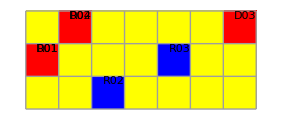

```mathematica
wd=SyncWorldUpdate[wd,{Moore,2},DInt,Fix]
DisplayWorld[wd]
```

```mathematica
wd=RandomInitialWorld[3,5,5,5,F];
WriteWorld[wd,"t3.txt"];
Do[(wd =SyncWorldUpdate[wd,{Moore,2},DInt,Fix]; 
WriteWorld[wd,"t3.txt"]), {30}];
```

```mathematica
AllAgentNames[ReadHistory["t3.txt"]⟦1⟧]
```

{D01,D02,D03,R01,R02,R03,R04}

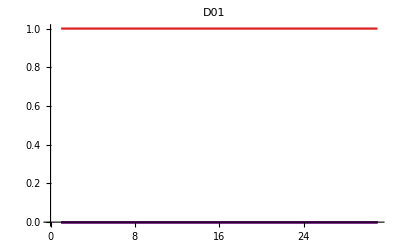
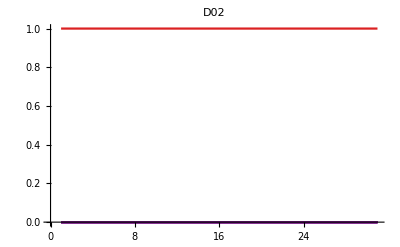
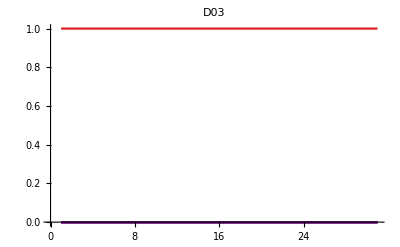
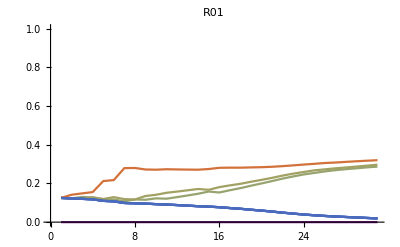
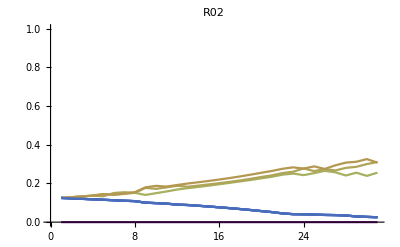
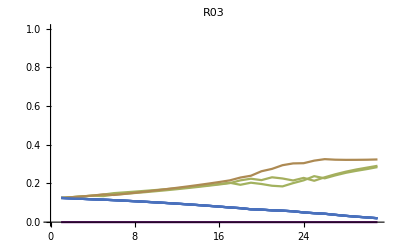
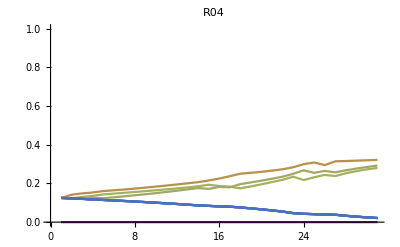

```mathematica
PlotAgentsProbHist["t3.txt",{}]
```

```mathematica
wd=RandomInitialWorld[3,8,8,5,F];
WriteWorld[wd,"t1.txt"];
Timing[Do[(wd =SyncWorldUpdate[wd,{Moore,2},DInt,Fix]; 
WriteWorld[wd,"t1.txt"]), {1000}];]
```

{25.4164,Null}

```mathematica
DisplayHistory["t1.txt",{1,10},{}]
```

```mathematica
ConvergedAgents["sync_test.txt",0.47]
```

{{D01,1},{D02,1},{D03,1},{D04,1},{D05,1},{D06,1},{R01,200},{R02,349},{R03,404},{R04,71},{R05,214},{R06,30},{R07,331},{R08,73},{R09,212},{R10,237},{R11,98},{R12,228},{R13,244},{R14,233}}

```mathematica
ReadHistory["t3.txt",{1,1,1}]
```

{{{{D01,{0.,0.,0.,0.,1.,0.,0.,0.,0.},{{0,0,0,0,1000,0,0,0,0}}},{4,2}},{{D02,{0.,0.,0.,0.,0.,0.,0.,1.,0.},{{0,0,0,0,0,0,0,1000,0}}},{4,3}},{{D03,{0.,0.,0.,1.,0.,0.,0.,0.,0.},{{0,0,0,1000,0,0,0,0,0}}},{3,5}},{{R01,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{{0,0,0,0,0,0,0,0,0}}},{5,5}},{{R02,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{{0,0,0,0,0,0,0,0,0}}},{1,5}},{{R03,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{{0,0,0,0,0,0,0,0,0}}},{3,2}},{{R04,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{{0,0,0,0,0,0,0,0,0}}},{4,5}},{{R05,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{{0,0,0,0,0,0,0,0,0}}},{2,5}}},{5,5},{dd,RR,dR,Rd},F}

```mathematica
ConvergedAgents["t3.txt",0.15]
```

{{D01,1},{D02,1},{D03,1}}

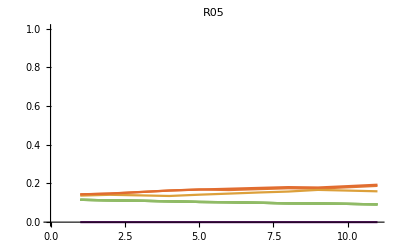

```mathematica
PlotAgentsProbHist["t1.txt",{5,15},{R05}]
```

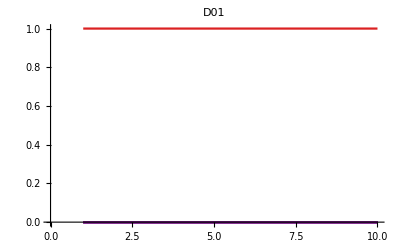
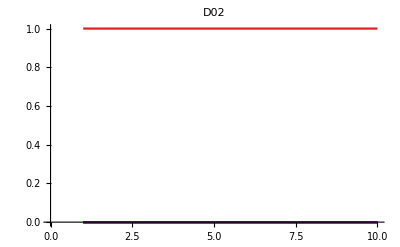
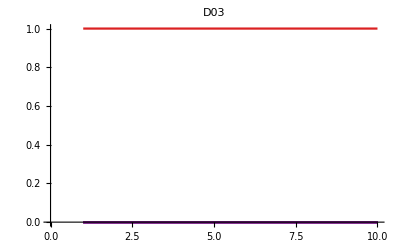
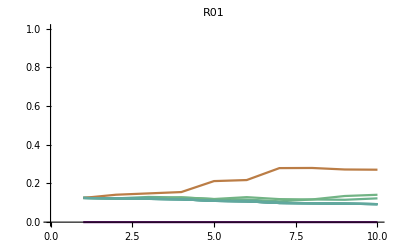
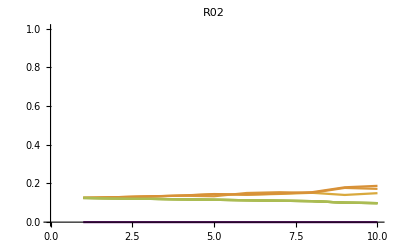
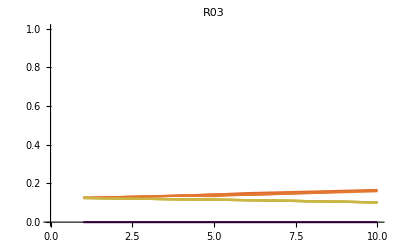
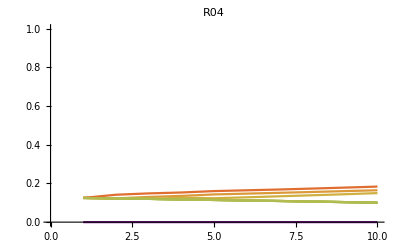

```mathematica
PlotAgentsProbHist["t3.txt",{1,10}]
```

```mathematica
DefineTransPotFunction[F];
Plot[TransPotFunction[x,10,9,100],{x,1,100}]
```

```mathematica
GetWorldInHistory["t3.txt",1]
```

{{{{D01,{0.,1.,0.,0.,0.,0.,0.,0.,0.},{{0,1000,0,0,0,0,0,0,0}}},{1,29}},{{R01,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{{0,0,0,0,0,0,0,0,0}}},{1,10}},{{R02,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{{0,0,0,0,0,0,0,0,0}}},{1,30}},{{R03,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.},{{0,0,0,0,0,0,0,0,0}}},{1,13}}},{1,30},{dd,RR,dR,Rd},F}

```mathematica
w1d=RandomInitialWorld[2,4,20,1,F];
WriteWorld[w1d,"t5.txt"];
Do[(w1d =SyncWorldUpdate[w1d,{Moore,1},DInt,Fix]; 
WriteWorld[w1d,"t5.txt"]), {100}];
```

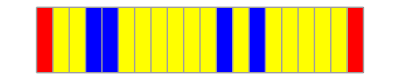
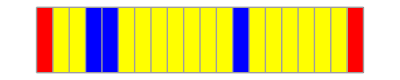
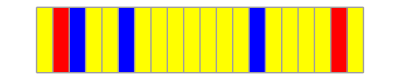
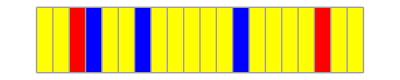
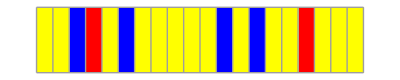
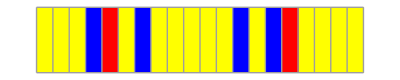
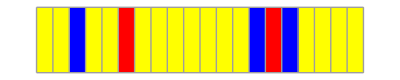
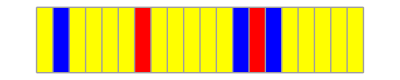
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
DisplayHistory["t5.txt",{1,100},{}]
```

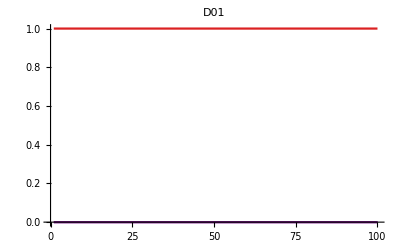
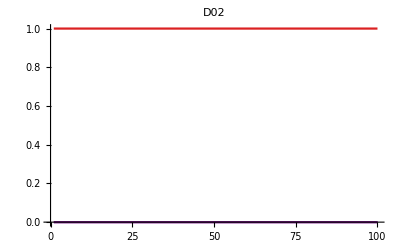
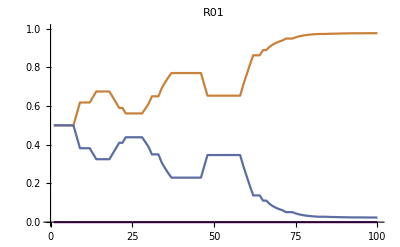
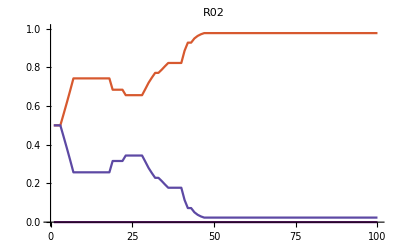
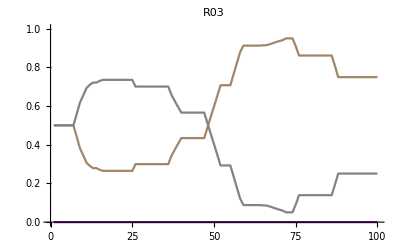
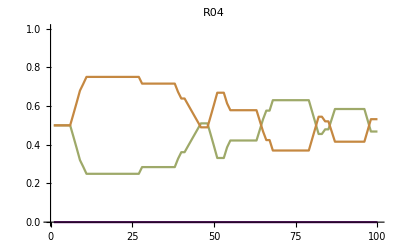

```mathematica
PlotAgentsProbHist["t5.txt",{1,100}]
```

```mathematica
MultipleRuns[fninit_Integer:1,fnfinal_Integer:1]:=
(Do[
wd=RandomInitialWorld[3,15,12,10,F];
WriteWorld[wd,ToString[fn]<>".txt"];
Do[(wd =SyncWorldUpdate[wd,{Moore,2},DInt,Fix]; 
WriteWorld[wd,ToString[fn]<>".txt"]), {9}],
{fn,fninit,fnfinal}])
```